```mathematica
Δ=1;ω=2;
d2[k_]:=Integrate[Sin[ω*t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
d22[k_]=d2[k]*Conjugate[d2[k]]
```

1/36 (4-ⅇ^(-ⅈ k) (3+ⅇ^(4 ⅈ k))) (4-ⅇ^(ⅈ Conjugate[k]) (3+ⅇ^(-4 ⅈ Conjugate[k])))

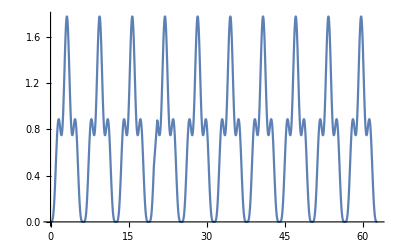

```mathematica
Plot[d22[k],{k,0,20*π}]
```

```mathematica
Block[{x},Do[f[i][x_]=(((Sign[x]+1)/2.0) -((Sign[x-(2*i)*π/Δ]+1)/2.0))*Sin[ω*x]
,{i,1,10}]]
```

```mathematica
Definition @ f
```

f[1][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-2 π+x])) Sin[2 x]
 
f[2][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-4 π+x])) Sin[2 x]
 
f[3][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-6 π+x])) Sin[2 x]
 
f[4][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-8 π+x])) Sin[2 x]
 
f[5][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-10 π+x])) Sin[2 x]
 
f[6][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-12 π+x])) Sin[2 x]
 
f[7][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-14 π+x])) Sin[2 x]
 
f[8][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-16 π+x])) Sin[2 x]
 
f[9][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-18 π+x])) Sin[2 x]
 
f[10][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[-20 π+x])) Sin[2 x]

```mathematica
Block[{t},g[t_]=Piecewise[Table[{f[i][t],(i-1)*π<t<i*2*π},{i,10}]]];
```

```mathematica
Definition @ g
```

g[t_]=Piecewise[{{(0.5 (1+Sign[t])-0.5 (1+Sign[-2 π+t])) Sin[2 t], 0<t<2 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-4 π+t])) Sin[2 t], π<t<4 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-6 π+t])) Sin[2 t], 2 π<t<6 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-8 π+t])) Sin[2 t], 3 π<t<8 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-10 π+t])) Sin[2 t], 4 π<t<10 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-12 π+t])) Sin[2 t], 5 π<t<12 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-14 π+t])) Sin[2 t], 6 π<t<14 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-16 π+t])) Sin[2 t], 7 π<t<16 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-18 π+t])) Sin[2 t], 8 π<t<18 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-20 π+t])) Sin[2 t], 9 π<t<20 π}, {0, True}}]

```mathematica
l2[k_]:=Integrate[g[t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
l22[k_]=l2[k]*Conjugate[l2[k]]
```

Conjugate[Piecewise[{{-0.166667 ⅇ^((0.-1. ⅈ) k) (-1.+ⅇ^((0.+1. ⅈ) k))^2 (3.+2. ⅇ^((0.+1. ⅈ) k)+ⅇ^((0.+2. ⅈ) k)), k≤62.8319}, {0., True}}]] (Piecewise[{{-0.166667 ⅇ^((0.-1. ⅈ) k) (-1.+ⅇ^((0.+1. ⅈ) k))^2 (3.+2. ⅇ^((0.+1. ⅈ) k)+ⅇ^((0.+2. ⅈ) k)), k≤62.8319}, {0., True}}])

```mathematica
Plot[l22[k],{k,0,20*π}]
```

-Graphics-

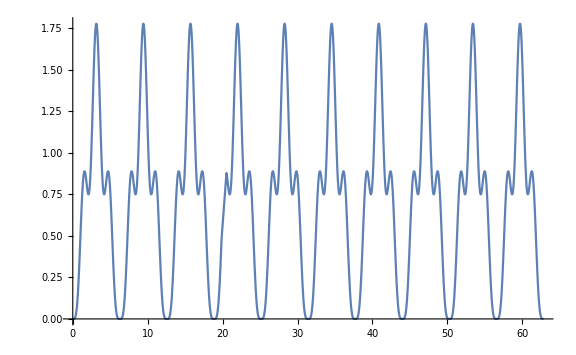

```mathematica
Show[%12,ImageSize->Large]
```

```mathematica
ω=0.9;Δ=1;
```

```mathematica
Block[{x},Do[f1[i][x_]=(((Sign[x]+1)/2.0) -((Sign[x-(2*i)*π/Δ]+1)/2.0))*Sin[ω*x]
,{i,1,10}]]
```

```mathematica
Definition @ f1
```

f1[1][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(2 π)/Δ])) Sin[0.9 x]
 
f1[2][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(4 π)/Δ])) Sin[0.9 x]
 
f1[3][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(6 π)/Δ])) Sin[0.9 x]
 
f1[4][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(8 π)/Δ])) Sin[0.9 x]
 
f1[5][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(10 π)/Δ])) Sin[0.9 x]
 
f1[6][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(12 π)/Δ])) Sin[0.9 x]
 
f1[7][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(14 π)/Δ])) Sin[0.9 x]
 
f1[8][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(16 π)/Δ])) Sin[0.9 x]
 
f1[9][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(18 π)/Δ])) Sin[0.9 x]
 
f1[10][x_]=(0.5 (1+Sign[x])-0.5 (1+Sign[x-(20 π)/Δ])) Sin[0.9 x]

```mathematica
Block[{t},g1[t_]=Piecewise[Table[{f1[i][t],(i-1)*π<t<i*2*π},{i,10}]]];
```

```mathematica
Definition @ g1
```

g1[t_]=Piecewise[{{(0.5 (1+Sign[t])-0.5 (1+Sign[t-(2 π)/Δ])) Sin[0.9 t], 0<t<2 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(4 π)/Δ])) Sin[0.9 t], π<t<4 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(6 π)/Δ])) Sin[0.9 t], 2 π<t<6 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(8 π)/Δ])) Sin[0.9 t], 3 π<t<8 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(10 π)/Δ])) Sin[0.9 t], 4 π<t<10 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(12 π)/Δ])) Sin[0.9 t], 5 π<t<12 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(14 π)/Δ])) Sin[0.9 t], 6 π<t<14 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(16 π)/Δ])) Sin[0.9 t], 7 π<t<16 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(18 π)/Δ])) Sin[0.9 t], 8 π<t<18 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[t-(20 π)/Δ])) Sin[0.9 t], 9 π<t<20 π}, {0, True}}]

```mathematica
h2[k_]:=Integrate[g1[t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
h22[k_]=h2[k]*Conjugate[h2[k]]
```

Conjugate[Piecewise[{{-0.263158 (-1.+ⅇ^((0.+0.1 ⅈ) k))^2 (18.+17. ⅇ^((0.+0.1 ⅈ) k)+16. ⅇ^((0.+0.2 ⅈ) k)+15. ⅇ^((0.+0.3 ⅈ) k)+14. ⅇ^((0.+0.4 ⅈ) k)+13. ⅇ^((0.+0.5 ⅈ) k)+12. ⅇ^((0.+0.6 ⅈ) k)+11. ⅇ^((0.+0.7 ⅈ) k)+10. ⅇ^((0.+0.8 ⅈ) k)+9. ⅇ^((0.+0.9 ⅈ) k)+8. ⅇ^((0.+1. ⅈ) k)+7. ⅇ^((0.+1.1 ⅈ) k)+6. ⅇ^((0.+1.2 ⅈ) k)+5. ⅇ^((0.+1.3 ⅈ) k)+4. ⅇ^((0.+1.4 ⅈ) k)+3. ⅇ^((0.+1.5 ⅈ) k)+2. ⅇ^((0.+1.6 ⅈ) k)+ⅇ^((0.+1.7 ⅈ) k)), k≤62.8319}, {0., True}}]] (Piecewise[{{-0.263158 (-1.+ⅇ^((0.+0.1 ⅈ) k))^2 (18.+17. ⅇ^((0.+0.1 ⅈ) k)+16. ⅇ^((0.+0.2 ⅈ) k)+15. ⅇ^((0.+0.3 ⅈ) k)+14. ⅇ^((0.+0.4 ⅈ) k)+13. ⅇ^((0.+0.5 ⅈ) k)+12. ⅇ^((0.+0.6 ⅈ) k)+11. ⅇ^((0.+0.7 ⅈ) k)+10. ⅇ^((0.+0.8 ⅈ) k)+9. ⅇ^((0.+0.9 ⅈ) k)+8. ⅇ^((0.+1. ⅈ) k)+7. ⅇ^((0.+1.1 ⅈ) k)+6. ⅇ^((0.+1.2 ⅈ) k)+5. ⅇ^((0.+1.3 ⅈ) k)+4. ⅇ^((0.+1.4 ⅈ) k)+3. ⅇ^((0.+1.5 ⅈ) k)+2. ⅇ^((0.+1.6 ⅈ) k)+ⅇ^((0.+1.7 ⅈ) k)), k≤62.8319}, {0., True}}])

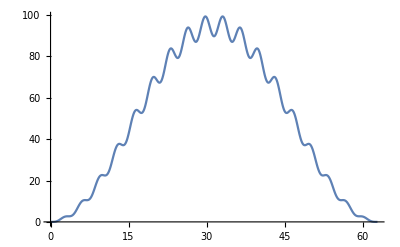

```mathematica
Plot[h22[k],{k,0,20*π}]
```